```mathematica
SetDirectory["/Users/mbibireata/Documents/GitHub/Networks/figures"]
```

/Users/mbibireata/Documents/GitHub/Networks/figures

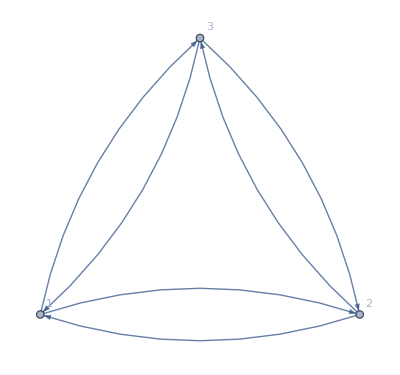

```mathematica
g1=Graph[{1->2,2->3,3->1,2->1,3->2,1->3},(*PlotLabel->"Directed 2-Core of Size 3",*)VertexLabels->Automatic]
```

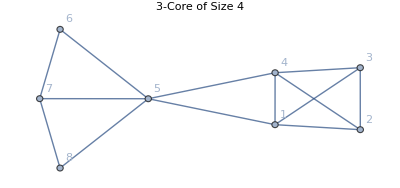

```mathematica
(* Graph with 4 vertices *) 
g2=Graph[{1<->2, 2<->3, 3<->4,1<->4, 1<->3, 2<->4, 4<->5, 1<->5, 5<->6, 6<->7, 7<->8, 8<->5, 7<->5},PlotLabel->"3-Core of Size 4",VertexLabels->Automatic]
```

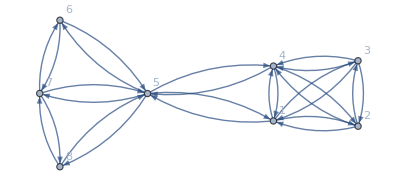

```mathematica
(* Same Graph but Directed *)
g2Prime = Graph[{1->2, 2->3, 3->4, 4->1, 2->1, 3->2, 3->4, 1->4,3->1, 1->3, 4->2, 2->4, 4->5, 5->4, 1->5, 5->1, 5->6, 6->5, 6->7, 7->6, 7->5,5->7, 7->8, 8->7, 8->5, 5->8}, VertexLabels->Automatic]
```

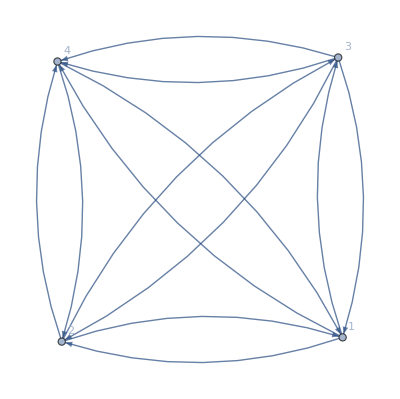

```mathematica
g3=Graph[{1->2, 2->3, 3->4, 4->1, 2->1, 3->2, 3->4, 1->4,3->1, 1->3, 4->2, 2->4},VertexLabels->Automatic]
```

```mathematica
Export["g1.png",g1]
Export["g2.png",g2Prime]
Export["g3.png",g3]
```

g1.png

g2.png

g3.png

(0 | 1 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

mat_test.png

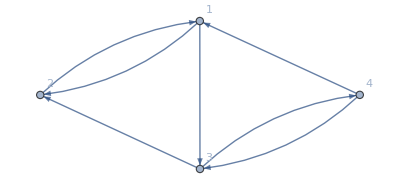

adj_mat_sample.png

```mathematica
(* Adjacency matrix to graph *) 
mat={{0,1,1,0},{1,0,0,0},{0,1,0,1},{1,0,1,0}};
mat//MatrixForm
Export["mat_test.png",mat//MatrixForm]
g4=AdjacencyGraph[mat,VertexLabels->Automatic]
Export["adj_mat_sample.png",g4]
```

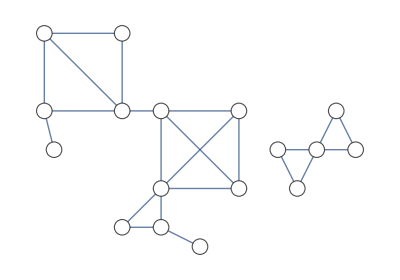

{VertexCoordinates→{{0.5,-0.5},{2.5,-0.5},{0.5,-2.5},{2.5,-2.5},{0.75,-3.5},{3.5,-2.5},{5.5,-2.5},{3.5,-4.5},{5.5,-4.5},{2.5,-5.5},{3.5,-5.5},{4.5,-6.},{6.5,-3.5},{7.5,-3.5},{8.,-2.5},{8.5,-3.5},{7.,-4.5}}}

1core.png

```mathematica
graphMapping1={
1<->2,1<->3,1<->4,
2<->4,
3<->4,3<->5,
4<->6,
6<->7,6<->8,6<->9,
7<->8,7<->9,
8<->9,8<->10,8<->11,
10<->11,
11<->12,
13 <->14, 
14<->15,
15<->16,
16<->14,
17<->13, 17<->14
};
coordMapping1={
{0.5,-0.5}, (* 1 *)
{2.5,-0.5}, (* 2 *)
{0.5, -2.5}, (* 3 *) 
{2.5, -2.5},(* 4 *)
{0.75, -3.5}, (* 5 *) 
{3.5,-2.5},
{5.5, -2.5},(* 7 *) 
{3.5, -4.5},
{5.5, -4.5},(* 9 *)
{2.5, -5.5},
{3.5, -5.5}, (* 11 *)
{4.5, -6.0},
{6.5,-3.5}, (* 13 *)
{7.5,-3.5},
{8.0,-2.5}, (* 15 *)
{8.5,-3.5},
{7.0,-4.5} (* 17 *)
};
panelLabel[lbl_]:=Panel[lbl,FrameMargins->5,Background->White];
(*Graph[graphMapping, VertexCoordinates->coordMapping, (*VertexLabels->Automatic,*)
VertexLabels->Table[i->Placed[i,Center,panelLabel],{i,17}],
VertexLabelStyle->Directive[15]
]*)
k1 = Graph[
graphMapping1, VertexCoordinates->coordMapping1,VertexSize->0.4, VertexStyle->White
]
AbsoluteOptions[%,VertexCoordinates]
Export["1core.png",k1]
```

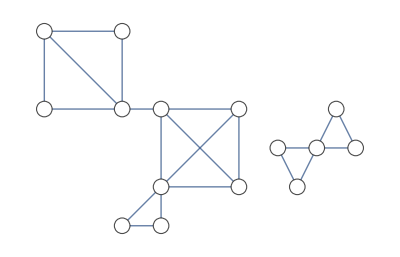

2core.png

```mathematica
graphMapping2 = {
1<->2,1<->3,1<->4,
2<->4,
3<->4,
4<->6,
6<->7,6<->8,6<->9,
7<->8,7<->9,
8<->9,8<->10,8<->11,
10<->11,
13 <->14, 
14<->15,
15<->16,
16<->14,
17<->13, 17<->14
};
coordMapping2={
{0.5,-0.5}, (* 1 *)
{2.5,-0.5}, (* 2 *)
{0.5, -2.5}, (* 3 *) 
{2.5, -2.5},(* 4 *)
{3.5,-2.5},
{5.5, -2.5},(* 7 *) 
{3.5, -4.5},
{5.5, -4.5},(* 9 *)
{2.5, -5.5},
{3.5, -5.5}, (* 11 *)
{6.5,-3.5}, (* 13 *)
{7.5,-3.5},
{8.0,-2.5}, (* 15 *)
{8.5,-3.5},
{7.0,-4.5} (* 17 *)
};
k2 = Graph[
graphMapping2, VertexCoordinates->coordMapping2,VertexSize->0.4, VertexStyle->White
]
Export["2core.png",k2]
```

{{3.5,-2.5},{5.5,-2.5},{3.5,-4.5},{5.5,-4.5}}

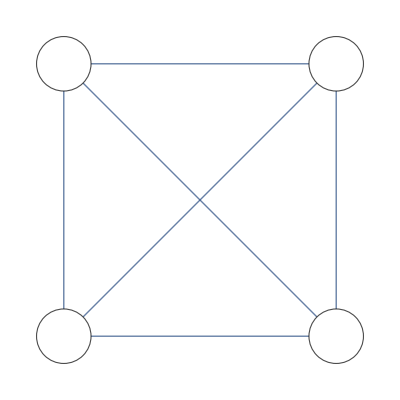

```mathematica
graphMapping3 = {
1<->2,1<->3,1<->4,
2<->3,2<->4,
3<->4
};
coordMapping3={
{3.5,-2.5},
{5.5, -2.5},(* 7 *) 
{3.5, -4.5},
{5.5, -4.5}(* 9 *)
}
k3 = Graph[
graphMapping3,VertexCoordinates->coordMapping3, VertexSize->0.2, VertexStyle->{White}, EdgeStyle->Thick
]
(*Export["3core.png",k3]*)
```

```mathematica
Export["1core.png",k1,ImageResolution->500]
Export["2core.png",k2,ImageResolution->500]
Export["3core.png",k3,ImageResolution->500]
```

1core.png

2core.png

3core.png

```mathematica
Export["3core.png",k3,ImageResolution->1000]
```

3core.png